```mathematica
ParseFile[filename_String]:=StringDelete[ToLowerCase[ReadString[filename]], PunctuationCharacter];
```

```mathematica
wordsGood =  ParseFile["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/WordsPositive.txt"];
wordsBad = ParseFile["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/WordsNegative.txt"];
embedding=NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"];
```

```mathematica
TrainModel :=[]
embedding[wordsGood]
```

{{0.86323,0.031356,0.10169,0.26639,0.19313,-0.076727,-0.22647,-0.69596,-0.63946,-0.8632,-0.29465,-0.31175,77,0.4905,0.45353,0.13881,0.091135,0.31961,-0.077948,0.045671,-0.55133,-0.28853,-0.50833,-0.31382},2004,{1}}
 |  |  |  |

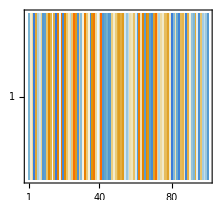

```mathematica
MatrixPlot[%]
```

```mathematica
Dimensions[%142]
```

{2006,100}

```mathematica
SentimentFromEmbeddings[sentence_String] := Module[{cntGood, cntBad, wordsInput, cntAll, resultPositivness, resultCertainity},
wordsGood = StringSplit[ReadString["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/WordsPositive.txt"]];
wordsBad = StringSplit[ReadString["/Users/ashvardanian/CodeMine/WolframSummer19/Final Project/Drafts/WordsNegative.txt"]];
embedding=NetModel["GloVe 100-Dimensional Word Vectors Trained on Tweets"];
Map[embedding, wordsGood];

wordsInput = StringSplit[sentence];
cntAll = Length[wordsInput];
cntGood = Length[Intersection[wordsGood, wordsInput]];
cntBad = Length[Intersection[wordsBad, wordsInput]];
resultCertainity = (cntGood + cntBad) / cntAll;
resultPositivness = 0.5 - (cntBad / cntAll) + (cntGood / cntAll);
{ resultPositivness, resultCertainity }
];
```

```mathematica
SentimentFromWordLists[inputQuery]
```

{0.653846,2/13}